```mathematica
Quit[];
```

```mathematica
$LoadAddOns = {"FeynArts","FeynHelpers"};
<< FeynCalc`
$FAVerbose = 0;
```

FeynCalc 10.0.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

```mathematica
FAPatch[PatchModelsOnly->True,FAModelsDirectory->FileNameJoin[{NotebookDirectory[],"Two_Fermions_FA"}]]
```

Successfully patched FeynArts.

```mathematica
FCClearScalarProducts[];
SP[p,p]=s;
```

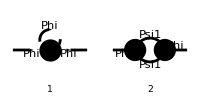

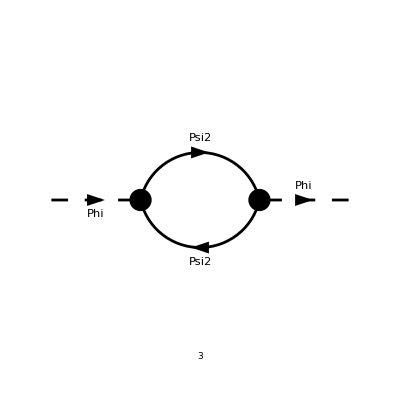

{-(ⅈ lambda4)/(16 π^4 (q^2-mPhi^2)),-(ⅈ tr((mPsi1-γ·q).(-Im(Y1)-ⅈ Re(Y1)).(mPsi1+γ·(p-q)).(Im(Y1)-ⅈ Re(Y1))))/(16 π^4 (q^2-mPsi1^2).((q-p)^2-mPsi1^2)),-(ⅈ tr((mPsi2-γ·q).(-Im(Y2)-ⅈ Re(Y2)).(mPsi2+γ·(p-q)).(Im(Y2)-ⅈ Re(Y2))))/(16 π^4 (q^2-mPsi2^2).((q-p)^2-mPsi2^2))}

```mathematica
LoopDiags = InsertFields[CreateTopologies[1, 1 -> 1, ExcludeTopologies->{Tadpoles,WFCorrections}],S[1]->S[1], InsertionLevel->{Particles},ExcludeParticles->{},Model -> FileNameJoin[{NotebookDirectory[],"Two_Fermions_FA", "Two_Fermions_FA"}], GenericModel -> FileNameJoin[{NotebookDirectory[],"Two_Fermions_FA", "Two_Fermions_FA"}]];
Paint[LoopDiags, Numbering->Simple, SheetHeader->None,ColumnsXRows->{2,1},ImageSize->{200,100}];
AmpLoop[0]=(Contract/@FCFAConvert[CreateFeynAmp[LoopDiags],IncomingMomenta->{p},OutgoingMomenta->{p},LoopMomenta->{q},ChangeDimension->D,DropSumOver->True,UndoChiralSplittings->True,SMP->True,FinalSubstitutions->M$FACouplings])/.{Y1r->Re[Y1],Y1i->Im[Y1],Y2r->Re[Y2],Y2i->Im[Y2]}
```

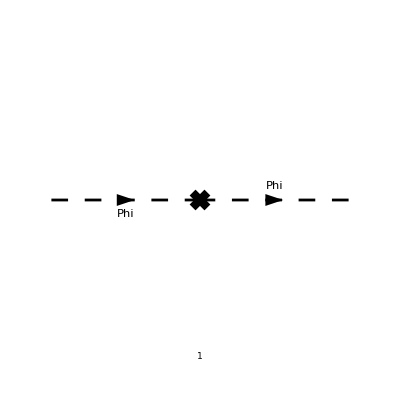

```mathematica
CTDiags = InsertFields[CreateCTTopologies[1, 1 -> 1,ExcludeTopologies->{Tadpoles,WFCorrectionCTs}],S[1]->S[1], InsertionLevel->{Particles}, Model -> FileNameJoin[{NotebookDirectory[],"Two_Fermions_FA", "Two_Fermions_FA"}], GenericModel -> FileNameJoin[{NotebookDirectory[],"Two_Fermions_FA", "Two_Fermions_FA"}]];
Paint[CTDiags, Numbering->Simple, SheetHeader->None,ColumnsXRows->{2,1},ImageSize->{200,100}];
AmpCT[0]=Contract/@FCFAConvert[CreateFeynAmp[CTDiags],IncomingMomenta->{p},OutgoingMomenta->{p},ChangeDimension->D,DropSumOver->True,UndoChiralSplittings->True,SMP->True,FinalSubstitutions->M$FACouplings];
```

```mathematica
Const1[x_]:=1;
Const0[x_]:=0;
evalLoop[ex_]:=ex//TID[#,q,ToPaVe->True]&//DotSimplify[#,Expanding->False]&//DiracSimplify[#,DiracSubstitute67->True]&//Collect2[#,{A0,B0,C0,D0}]&;
processLoop[exs_]:=(
a1=FCTraceFactor/@DotSimplify[#,Expanding->False]&/@exs;
a2=evalLoop/@a1;
a3=Total[a2];
a4=ChangeDimension[PaXEvaluate[a3],4]//Expand
)
```

```mathematica
AmpLoop[1]=AmpLoop[0]//processLoop;
AmpTotal[0]=(AmpLoop[1]+Total[AmpCT[0]])//Expand;
```

Get::noopen: Cannot open C:\Users\hypercube256\AppData\Roaming\Mathematica\Applications\X\PacletInfo.m.

Part::partd: Part specification $Failed⟦2⟧ is longer than depth of object.

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[2,FeynCalc`PackageX`Private`n1__~~.~~FeynCalc`PackageX`Private`n2__~~.~~FeynCalc`PackageX`Private`n3__:>{FeynCalc`PackageX`Private`n1,FeynCalc`PackageX`Private`n2,FeynCalc`PackageX`Private`n3}].

Identity::argx: Identity called with 2 arguments; 1 argument is expected.

ToExpression::notstrbox: FeynCalc`PackageX`Private`n1__~~.~~FeynCalc`PackageX`Private`n2__~~.~~FeynCalc`PackageX`Private`n3__:>{FeynCalc`PackageX`Private`n1,FeynCalc`PackageX`Private`n2,FeynCalc`PackageX`Private`n3} is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Identity::argx: Identity called with 2 arguments; 1 argument is expected.

```mathematica
RNCond1=Simplify[AmpTotal[0]/.{s->mPhi^2},Assumptions->mPhi>0]//Re//ComplexExpand//Refine[#,Assumptions->{mPhi>2mPsi1>2mPsi2>0}]&;
RNCond2=Simplify[D[AmpTotal[0],s]/.{s->mPhi^2},Assumptions->mPhi>0]//Re//ComplexExpand//Refine[#,Assumptions->{mPhi>2mPsi1>2mPsi2>0}]&;
RNRes=Solve[{RNCond1==0,RNCond2==0},{FR$delta({mPhi},{}),FR$deltaZ({Phi,Phi},{{}})}];
```

```mathematica
AmpTotal[1]=(AmpTotal[0]/.RNRes[[1]])/.ScaleMu->1//ComplexExpand//Refine[#,Assumptions->{mPhi>2mPsi1>2mPsi2>0,s∈Reals}]&//FullSimplify;
```

```mathematica
AmpTotal[2]=AmpTotal[1]/.{mPhi->1,mPsi1->0.45,mPsi2->0.1,Y1^2->2,Y2^2->4.7};
AmpBGTotal[2]=AmpTotal[1]/.{mPhi->1,mPsi1->0.45,mPsi2->0.1,Y1^2->0,Y2^2->4.7};
```

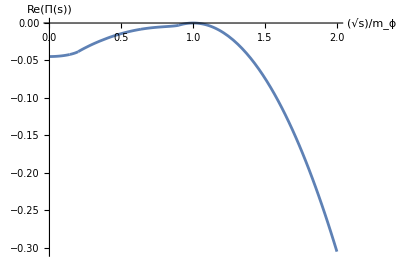

```mathematica
Show[ParametricPlot[{Sqrt[s],Re[AmpTotal[2]]},{s,0,4},PlotRange->Full,MaxRecursion->10,AxesLabel->{Sqrt[s]/Subscript[m, ϕ],Re[Π[s]]}],AspectRatio->0.7]
```

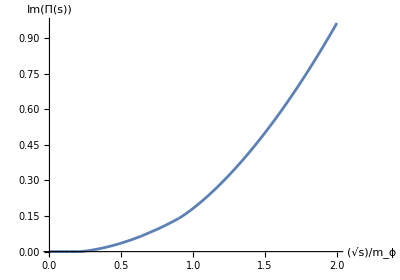

```mathematica
Show[ParametricPlot[{Sqrt[s],Im[AmpTotal[2]]},{s,0,4},PlotRange->Full,MaxRecursion->10,AxesLabel->{Sqrt[s]/Subscript[m, ϕ],Im[Π[s]]}],AspectRatio->0.7]
```

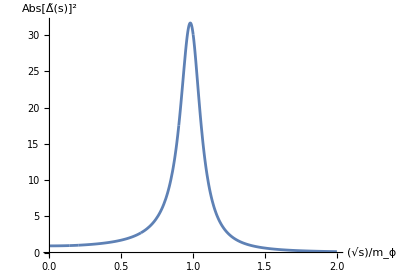

```mathematica
Show[ParametricPlot[{Sqrt[s],Abs[s-1+AmpTotal[2]]^-2},{s,0,4},PlotRange->Full,MaxRecursion->10,AxesLabel->{Sqrt[s]/Subscript[m, ϕ],Abs[OverTilde[Δ][s]]^2}],AspectRatio->0.7]
```

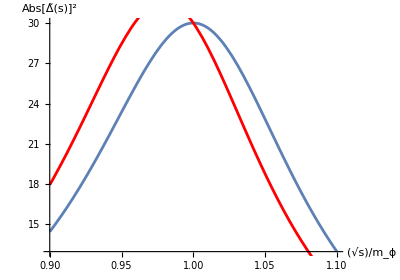

```mathematica
Γ=Im[AmpTotal[2]]/.s->1;
Show[ParametricPlot[{x,((x^2-1)^2+Γ^2)^-1},{x,0.9,1.1},PlotRange->Full,MaxRecursion->10,AxesLabel->{Sqrt[s]/Subscript[m, ϕ],Abs[OverTilde[Δ][s]]^2}],ParametricPlot[{x,((x^2-1)^2+(Im[AmpTotal[2]]/.s->x^2)^2)^-1},{x,0.9,1.1},PlotRange->Full,MaxRecursion->10,PlotStyle->{Red}],AspectRatio->0.7]
```

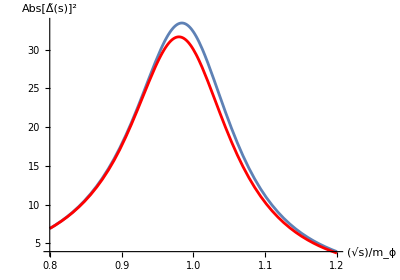

```mathematica
Show[ParametricPlot[{x,(Abs[s-1+AmpBGTotal[2]]^-2)/.s->x^2},{x,0.8,1.2},PlotRange->Full,MaxRecursion->10,AxesLabel->{Sqrt[s]/Subscript[m, ϕ],Abs[OverTilde[Δ][s]]^2}],ParametricPlot[{x,(Abs[s-1+AmpTotal[2]]^-2)/.s->x^2},{x,0.8,1.2},PlotRange->Full,MaxRecursion->10,PlotStyle->{Red}],AspectRatio->0.7]
```

```mathematica
AmpTotal[3]=(AmpTotal[0]/.RNRes[[1]])/.{ScaleMu->1,tau2->0}//Refine[#,Assumptions->{mPhi>2mChi>0,0<s<4mChi^2}]&//Expand//FullSimplify[#,Assumptions->{mPhi>2mChi>0,0<s<4mChi^2}]&
```

1/(288 π^2 mPhi^3 s √(mPhi^2-4 mChi^2))(mPhi s √(mPhi^2-4 mChi^2) (√3 π lambda3^2 (5 mPhi^2-2 s)-9 (lambda3^2+2 tau1^2) (mPhi^2-s))+9 ⅈ mPhi^3 (lambda3^2 √(s (mPhi^2-4 mChi^2) (4 mPhi^2-s)) log((ⅈ √(s (4 mPhi^2-s))+2 mPhi^2-s)/(2 mPhi^2))+2 tau1^2 √(s (mPhi^2-4 mChi^2) (4 mChi^2-s)) log((ⅈ √(s (4 mChi^2-s))+2 mChi^2-s)/(2 mChi^2)))-18 s tau1^2 (2 mChi^2 (s-3 mPhi^2)+mPhi^4) log((mPhi (mPhi-√(mPhi^2-4 mChi^2)))/(2 mChi^2)-1))

```mathematica
Series[AmpTotal[3],{s,0,10},Assumptions->{mPhi>2mChi>0,0<s<4mChi^2}]//Simplify//Expand
```

((5 √3 π-27) lambda3^2-(18 tau1^2 (mPhi^2-6 mChi^2) log((mPhi (mPhi-√(mPhi^2-4 mChi^2)))/(2 mChi^2)-1))/(mPhi √(mPhi^2-4 mChi^2))-54 tau1^2)/(288 π^2)+(s ((21-4 √3 π) lambda3^2 mChi^2 mPhi+6 mPhi tau1^2 (6 mChi^2+mPhi^2)-(72 mChi^4 tau1^2 log((mPhi (mPhi-√(mPhi^2-4 mChi^2)))/(2 mChi^2)-1))/(√(mPhi^2-4 mChi^2))))/(576 π^2 mChi^2 mPhi^3)+(s^2 (lambda3^2 mChi^4+2 mPhi^4 tau1^2))/(1920 π^2 mChi^4 mPhi^4)+(s^3 (lambda3^2 mChi^6+2 mPhi^6 tau1^2))/(13440 π^2 mChi^6 mPhi^6)+(s^4 (lambda3^2 mChi^8+2 mPhi^8 tau1^2))/(80640 π^2 mChi^8 mPhi^8)+(s^5 (lambda3^2 mChi^10+2 mPhi^10 tau1^2))/(443520 π^2 mChi^10 mPhi^10)+(s^6 (lambda3^2 mChi^12+2 mPhi^12 tau1^2))/(2306304 π^2 mChi^12 mPhi^12)+(s^7 (lambda3^2 mChi^14+2 mPhi^14 tau1^2))/(11531520 π^2 mChi^14 mPhi^14)+(s^8 (lambda3^2 mChi^16+2 mPhi^16 tau1^2))/(56010240 π^2 mChi^16 mPhi^16)+(s^9 (lambda3^2 mChi^18+2 mPhi^18 tau1^2))/(266048640 π^2 mChi^18 mPhi^18)+(s^10 (lambda3^2 mChi^20+2 mPhi^20 tau1^2))/(1241560320 π^2 mChi^20 mPhi^20)+O(s^(21/2))

```mathematica
Series[AmpTotal[3],{s,0,4},Assumptions->{mPhi>2mChi>0,0<s<4mChi^2}]/.{mPhi->1,mChi->0.14,lambda3->0.15,tau1->0.13}
```

0.0988337+1.60692 s+(7.23826+0. ⅈ) s^2+(52.7438+0. ⅈ) s^3+(448.499+0. ⅈ) s^4+O(s^(9/2))

```mathematica
Series[1/(s-1+AmpTotal[3]),{s,0,4},Assumptions->{mPhi>2mChi>0,0<s<4mChi^2}]/.{mPhi->1,mChi->0.14,lambda3->0.15,tau1->0.13}
```

-1.10967-3.21009 s-(18.1992+0. ⅈ) s^2-(143.378+0. ⅈ) s^3-(1301.1+0. ⅈ) s^4+O(s^(9/2))

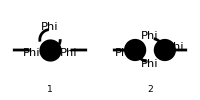

```mathematica
SelfLoopDiags = InsertFields[CreateTopologies[1, 1 -> 1, ExcludeTopologies->{Tadpoles,WFCorrections}],S[1]->S[1], InsertionLevel->{Particles},ExcludeParticles->{S[2],F[1],F[2]},Model -> FileNameJoin[{NotebookDirectory[],"Simple_Yukawa_FA", "Simple_Yukawa_FA"}], GenericModel -> FileNameJoin[{NotebookDirectory[],"Simple_Yukawa_FA", "Simple_Yukawa_FA"}]];
Paint[SelfLoopDiags, Numbering->Simple, SheetHeader->None,ColumnsXRows->{2,1},ImageSize->{200,100}];
AmpSelfLoop[0]=Contract/@FCFAConvert[CreateFeynAmp[SelfLoopDiags,Truncated->True,PreFactor->1],IncomingMomenta->{p},OutgoingMomenta->{p},LoopMomenta->{q},ChangeDimension->D,DropSumOver->True,UndoChiralSplittings->True,SMP->True,FinalSubstitutions->M$FACouplings]/(2π)^4;
```

```mathematica
AmpSelfLoop[1]=AmpSelfLoop[0]//processLoop;
AmpSelfTotal[0]=(AmpSelfLoop[1]+Total[AmpCT[0]])/ⅈ//Expand;
```

Get::noopen: Cannot open C:\Users\hypercube256\AppData\Roaming\Mathematica\Applications\X\PacletInfo.m.

Part::partd: Part specification $Failed⟦2⟧ is longer than depth of object.

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[2,FeynCalc`PackageX`Private`n1__~~.~~FeynCalc`PackageX`Private`n2__~~.~~FeynCalc`PackageX`Private`n3__:>{FeynCalc`PackageX`Private`n1,FeynCalc`PackageX`Private`n2,FeynCalc`PackageX`Private`n3}].

Identity::argx: Identity called with 2 arguments; 1 argument is expected.

ToExpression::notstrbox: FeynCalc`PackageX`Private`n1__~~.~~FeynCalc`PackageX`Private`n2__~~.~~FeynCalc`PackageX`Private`n3__:>{FeynCalc`PackageX`Private`n1,FeynCalc`PackageX`Private`n2,FeynCalc`PackageX`Private`n3} is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Identity::argx: Identity called with 2 arguments; 1 argument is expected.

```mathematica
RNSelfCond1=Simplify[AmpSelfTotal[0]/.{s->mPhi^2},Assumptions->mPhi>0]//Re//ComplexExpand//Refine[#,Assumptions->{mPhi>0}]&;
RNSelfCond2=Simplify[D[AmpSelfTotal[0],s]/.{s->mPhi^2},Assumptions->mPhi>0]//Re//ComplexExpand//Refine[#,Assumptions->{mPhi>0}]&;
RNSelfRes=Solve[{RNSelfCond1==0,RNSelfCond2==0},{FR$delta({mPhi},{}),FR$deltaZ({Phi,Phi},{{}})}];
```

```mathematica
AmpSelfTotal[1]=(AmpSelfTotal[0]/.RNSelfRes[[1]])/.ScaleMu->1//ComplexExpand//Refine[#,Assumptions->{mPhi>0,s∈Reals}]&//FullSimplify;
```

```mathematica
AmpSelfTotal[2]=AmpSelfTotal[1]/.{mPhi->1,lambda3->0.99};
```

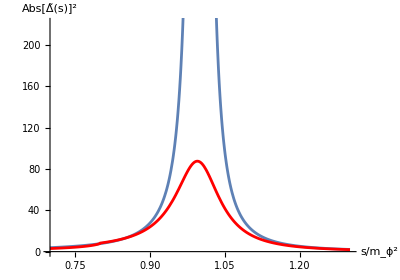

```mathematica
Show[ParametricPlot[{x,(Abs[s-1+AmpSelfTotal[2]]^-2)/.s->x^2},{x,0.7,1.3},MaxRecursion->10,AxesLabel->{s/Subscript[m, ϕ]^2,Abs[OverTilde[Δ][s]]^2}],ParametricPlot[{x,(Abs[s-1+AmpTotal[2]]^-2)/.s->x^2},{x,0.7,1.3},PlotRange->Full,MaxRecursion->10,PlotStyle->{Red}],AspectRatio->0.7]
```

```mathematica
AmpSelfTotal[2]/.s->0.8
```

3.25485×10^-6+0. ⅈ

```mathematica
AmpTotal[2]/.s->0.8
```

0.00305218+0.0800733 ⅈ

```mathematica
RNCond1=Simplify[AmpTotal[0]/.{s->mPhi^2},Assumptions->mPhi>0]//Re//ComplexExpand//Refine[#,Assumptions->{2mChi>mPhi>mChi>0}]&;
RNCond2=Simplify[D[AmpTotal[0],s]/.{s->mPhi^2},Assumptions->mPhi>0]//Re//ComplexExpand//Refine[#,Assumptions->{2mChi>mPhi>mChi>0}]&;
RNRes=Solve[{RNCond1==0,RNCond2==0},{FR$delta({mPhi},{}),FR$deltaZ({Phi,Phi},{{}})}];
```

```mathematica
AmpTotal[1]=(AmpTotal[0]/.RNRes[[1]])/.ScaleMu->1//ComplexExpand//Refine[#,Assumptions->{mPhi>2mChi>0,s∈Reals}]&//FullSimplify;
```

```mathematica
AmpTotal[2]=AmpTotal[1]/.{mPhi->1,mChi->0.51,lambda3->0.99,tau1->3};
```

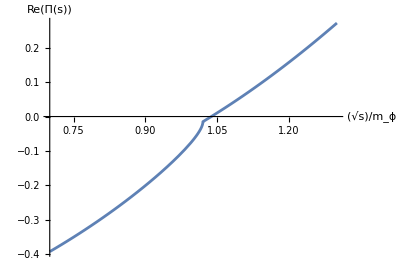

```mathematica
Show[ParametricPlot[{x,Re[AmpTotal[2]]/.s->x^2},{x,0.7,1.3},PlotRange->Full,MaxRecursion->10,AxesLabel->{Sqrt[s]/Subscript[m, ϕ],Re[Π[s]]}],AspectRatio->0.7]
```

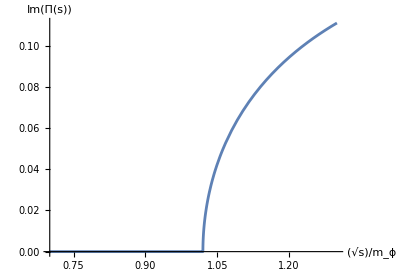

```mathematica
Show[ParametricPlot[{x,Im[AmpTotal[2]]/.s->x^2},{x,0.7,1.3},PlotRange->Full,MaxRecursion->10,AxesLabel->{Sqrt[s]/Subscript[m, ϕ],Im[Π[s]]}],AspectRatio->0.7]
```

```mathematica
Γ=Im[AmpTotal[2]]/.s->1;
Show[ParametricPlot[{x,((x^2-1)^2+Γ^2)^-1},{x,0.99999,1.00001},PlotRange->Full,MaxRecursion->10,AxesLabel->{s/Subscript[m, ϕ]^2,Abs[OverTilde[Δ][s]]^2}],ParametricPlot[{x,((x^2-1)^2+(Im[AmpTotal[2]]/.s->x^2)^2)^-1},{x,0.99999,1.00001},PlotRange->Full,MaxRecursion->10,AxesLabel->{s/Subscript[m, ϕ]^2,Abs[OverTilde[Δ][s]]^2},PlotStyle->{Red}],AspectRatio->0.7]
```

-Graphics-